# Infinite 3D medium, Delta Plane Source, Isotropic Scattering

## Exponential Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2016 Eugene d’Eon 
www.eugenedeon.com

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

α - single-scattering albedo
Σt - extinction coefficient
z - scalar position coordinate in medium (distance from plane source at origin)
u = cos θ - direction cosine
u_0 - direction cosine of emission

## Analytic Solutions

### Caseology quantities

```mathematica
CaseN0[c_,v0_]:=1/2 c v0^3 (c/(v0^2-1)-1/v0^2)
```

```mathematica
Casev0[c_?NumericQ]:=If[c<0.1,
1/(1-2 ⅇ^(-2/c) (1+((512-384 c+72 c^2-3 c^3) ⅇ^(-6/c))/(3 c^3)+((24-12 c+c^2) ⅇ^(-4/c))/c^2+((4-c) ⅇ^(-2/c))/c)),
FindRoot[c v ArcTanh[1/v]-1==0,{v,1+10^-14,10^14},Method->"Brent"][[1]][[2]]
]
```

```mathematica
CaseN[c_,v_]:=v (Caseλ[v,c]^2+((π c v)/2)^2)
```

```mathematica
Caseλ[v_,c_]:=1-c v ArcTanh[v]
```

```mathematica
Caseψ0[u_,v0_,c_,z_]:=c/2 v0/(v0-Sign[z]u)
```

### Rigorous diffusion approximation

```mathematica
inf3Ddeltaplaneisoscatter`ϕrigourousDiffusion[z_,Σt_,α_,u0_]:=Caseψ0[u0,#,α,z] E^(-Abs[z]Σt/#)/CaseN0[α,#]&[Casev0[α]]
```

### Fluence: exact solution

Fourier Transform:

```mathematica
inf3Ddeltaplaneisoscatter`ϕunscattered[z_,Σt_,u0_]:=ⅇ^(-(z Σt)/u0)/u0 Sign[z]HeavisideTheta[u0 Sign[z]]
```

```mathematica
inf3Ddeltaplaneisoscatter`ϕexact1[z_,Σt_,α_,u0_]:=inf3Ddeltaplaneisoscatter`ϕunscattered[z,Σt,u0]+α/Pi NIntegrate[(Cos[k z Σt]+k u0 Sin[k z Σt])/(1+k^2 u0^2)ArcTan[k]/(k-α ArcTan[k]),{k,0,Infinity}]
```

Caseology:

```mathematica
inf3Ddeltaplaneisoscatter`ϕexact2[z_,Σt_,α_,u0_]:=
If[z≥0,
inf3Ddeltaplaneisoscatter`ϕrigourousDiffusion[z,Σt,α,u0]+(Caseλ[u0,α] ⅇ^(-(Abs[z]Σt)/u0)/CaseN[α,u0] HeavisideTheta[1-u0] HeavisideTheta[u0]
+NIntegrate[ⅇ^(-(Abs[z]Σt)/v)/CaseN[α,v] α/2 v/(v-u0)
,{v,0,u0,1},Method->"PrincipalValue",PrecisionGoal->5]),
inf3Ddeltaplaneisoscatter`ϕexact2[-z,Σt,α,-u0]
]
```

### n-th scattered fluence: exact

Fourier Transform:

```mathematica
inf3Ddeltaplaneisoscatter`ϕexact[z_,Σt_,α_,u0_,n_]:=1/Pi NIntegrate[(Cos[k z Σt]+k u0 Sin[k z Σt])/(1+k^2 u0^2)(α ArcTan[k]/k)^n,{k,0,Infinity}]
```

### Radiance (exact)

Fourier Transform:

```mathematica
inf3Ddeltaplaneisoscatter`FourierLcollided[z_,k_,c_,u_,u0_]:=1/(2 Pi)c/(4 Pi)Exp[-I k z]/((1-I k u)(1-I k u0)(1- c ArcTan[k]/k))
```

```mathematica
inf3Ddeltaplaneisoscatter`LexactCollidedFourier[z_,u_,Σt_,α_,u0_]:=Re[NIntegrate[inf3Ddeltaplaneisoscatter`FourierLcollided[z Σt,k,α,u,u0]+inf3Ddeltaplaneisoscatter`FourierLcollided[z Σt,-k,α,u,u0],{k,0,Infinity}]]
```

Caseology:

```mathematica
inf3Ddeltaplaneisoscatter`LrigorousDiffusion[z_,u_,Σt_,α_,u0_]:=If[z>0,
1/(2 Pi)(Caseψ0[u0,#,α,z]Caseψ0[u,#,α,z]Exp[-Abs[z]/#])/CaseN0[α,#]&[Casev0[α]]
,inf3Ddeltaplaneisoscatter`Lexact[-z,-u,Σt,α,-u0]
]
```

## load MC data

```mathematica
inf3Ddeltaplaneisoscatter`ppoints[zs_,dz_,maxz_,Σt_]:=Table[{dz(i)-0.5dz-maxz,zs[[i]]/Σt},{i,1,Length[zs]}][[2;;-2]]
```

```mathematica
inf3Ddeltaplaneisoscatter`ppointsu[xs_,du_,Σt_]:=Table[{-1.0 +du(i)-0.5du,xs[[i]]/(2Σt)},{i,1,Length[xs]}][[1;;-1]]
```

```mathematica
inf3Ddeltaplaneisoscatter`fs=FileNames["code/3D_medium/infinite3Dmedium/deltaplanesource/data/inf3D_deltaplane_isotropicscatter*"];
```

```mathematica
inf3Ddeltaplaneisoscatter`index[x_]:=Module[{data,α,Σt,u0},
data=Import[x,"Table"];
Σt=data[[1,13]];
u0=data[[1,16]];
α=data[[2,3]];
{α,Σt,u0,data}];
inf3Ddeltaplaneisoscatter`simulations=inf3Ddeltaplaneisoscatter`index/@inf3Ddeltaplaneisoscatter`fs;
inf3Ddeltaplaneisoscatter`alphas=Union[#[[1]]&/@inf3Ddeltaplaneisoscatter`simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99}

```mathematica
inf3Ddeltaplaneisoscatter`muts=Union[#[[2]]&/@inf3Ddeltaplaneisoscatter`simulations]
```

{1}

```mathematica
inf3Ddeltaplaneisoscatter`u0s=Union[#[[3]]&/@inf3Ddeltaplaneisoscatter`simulations]
```

{0,0.5,1}

```mathematica
inf3Ddeltaplaneisoscatter`numcollorders=inf3Ddeltaplaneisoscatter`simulations[[1]][[4]][[2,13]];
inf3Ddeltaplaneisoscatter`maxz=inf3Ddeltaplaneisoscatter`simulations[[1]][[4]][[2,5]];inf3Ddeltaplaneisoscatter`dz=inf3Ddeltaplaneisoscatter`simulations[[1]][[4]][[2,7]];
inf3Ddeltaplaneisoscatter`numz=Floor[2inf3Ddeltaplaneisoscatter`maxz/inf3Ddeltaplaneisoscatter`dz];
```

## Compare Deterministic and MC

### Fluence - Exact solution 1 (Fourier Transform) comparison to MC

```mathematica
Clear[plota,plotmut,plotu0];
Manipulate[
If[Length[inf3Ddeltaplaneisoscatter`simulations]>0,
plota=α;
plotmut=Σt;
plotu0=u0;
,
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{{α,0.7},inf3Ddeltaplaneisoscatter`alphas},{{Σt,1},inf3Ddeltaplaneisoscatter`muts},{{u0,0.5},inf3Ddeltaplaneisoscatter`u0s}]
```

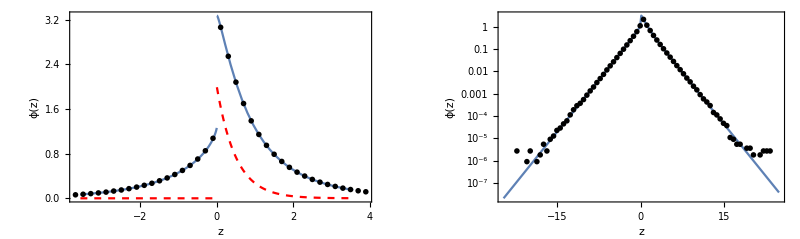

```mathematica
With[{u0=plotu0,α=plota,Σt=plotmut},
If[Length[inf3Ddeltaplaneisoscatter`simulations]>0,
Module[{data,maxz,dz,pointsϕ,plotpointsϕ,logplotϕ,plotϕ,exact1points,numpoints,skip},
data=SelectFirst[inf3Ddeltaplaneisoscatter`simulations,#[[1]]==α&&#[[2]]==Σt&&#[[3]]==u0&][[4]];
maxz=data[[2,5]];
dz=data[[2,7]];

pointsϕ = data[[4]];

(* divide by Σt to convert collision density into fluence *)
plotpointsϕ=inf3Ddeltaplaneisoscatter`ppoints[pointsϕ,dz,maxz,Σt];

exact1points=Quiet[{#[[1]], inf3Ddeltaplaneisoscatter`ϕexact1[#[[1]],Σt,α,u0]}]& /@plotpointsϕ;

numpoints=Length[plotpointsϕ];
skip=Floor[numpoints 6/7 1/2];

plotϕ=Quiet[Show[
Plot[inf3Ddeltaplaneisoscatter`ϕexact1[z,Σt,α,u0],{z,-maxz/7,maxz/7},PlotRange->All],
Plot[inf3Ddeltaplaneisoscatter`ϕunscattered[z,Σt,u0],{z,-maxz/7,maxz/7},PlotRange->All,PlotStyle->{Red,Dashed}],
ListPlot[plotpointsϕ[[skip;;-skip]],PlotRange->All,PlotStyle->{Black,PointSize[.01]}],
Frame->True,
FrameLabel->{{ ϕ[z],},{z,}},PlotRange->All
]];
logplotϕ=Quiet[Show[
ListLogPlot[exact1points,PlotRange->All,Joined->True],
ListLogPlot[plotpointsϕ[[1;;-1;;3]],PlotRange->All,PlotStyle->{Black,PointSize[.01]}],
Frame->True,
FrameLabel->{{ ϕ[z],},{z,}},PlotRange->All
]];
Show[GraphicsGrid[{{plotϕ,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution 1 (thin), Unscattered component (dashed)\nInfinite 3D, delta plane source, isotropic scattering, fluence ϕ[z], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", u_0 = "<>ToString[u0]]
]
,
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
]
```

### Fluence - Exact 2 (Caseology)

```mathematica
Clear[plota,plotmut,plotu0];
Manipulate[
If[Length[inf3Ddeltaplaneisoscatter`simulations]>0,
plota=α;
plotmut=Σt;
plotu0=u0;
,
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{{α,0.7},inf3Ddeltaplaneisoscatter`alphas},{{Σt,1},inf3Ddeltaplaneisoscatter`muts},{{u0,0.5},inf3Ddeltaplaneisoscatter`u0s}]
```

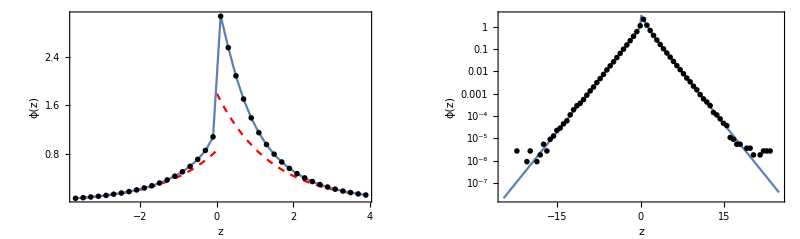

```mathematica
With[{u0=plotu0,α=plota,Σt=plotmut},
If[Length[inf3Ddeltaplaneisoscatter`simulations]>0,
Module[{data,maxz,dz,pointsϕ,plotpointsϕ,logplotϕ,plotϕ,exact1points,numpoints,skip},
data=SelectFirst[inf3Ddeltaplaneisoscatter`simulations,#[[1]]==α&&#[[2]]==Σt&&#[[3]]==u0&][[4]];
maxz=data[[2,5]];
dz=data[[2,7]];

pointsϕ = data[[4]];

(* divide by Σt to convert collision density into fluence *)
plotpointsϕ=inf3Ddeltaplaneisoscatter`ppoints[pointsϕ,dz,maxz,Σt];

exact1points=Quiet[{#[[1]], inf3Ddeltaplaneisoscatter`ϕexact2[#[[1]],Σt,α,u0]}]& /@plotpointsϕ;

numpoints=Length[plotpointsϕ];
skip=Floor[numpoints 6/7 1/2];

plotϕ=Quiet[Show[

Plot[inf3Ddeltaplaneisoscatter`ϕrigourousDiffusion[z,Σt,α,u0],{z,-maxz/7,maxz/7},PlotRange->All,PlotStyle->{Red,Dashed}],
ListPlot[exact1points[[skip;;-skip]],PlotRange->All,Joined->True],
ListPlot[plotpointsϕ[[skip;;-skip]],PlotRange->All,PlotStyle->{Black,PointSize[.01]}],
Frame->True,
FrameLabel->{{ ϕ[z],},{z,}},PlotRange->All
]];
logplotϕ=Quiet[Show[
ListLogPlot[exact1points,PlotRange->All,Joined->True],
ListLogPlot[plotpointsϕ[[1;;-1;;3]],PlotRange->All,PlotStyle->{Black,PointSize[.01]}],
Frame->True,
FrameLabel->{{ ϕ[z],},{z,}},PlotRange->All
]];
Show[GraphicsGrid[{{plotϕ,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution 2 (thin), rigorous diffusion (dashed)\nInfinite 3D, delta plane source, isotropic scattering, fluence ϕ[z], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", u_0 = "<>ToString[u0]]
]
,
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
]
```

### N-th scattered Fluence - Exact (Fourier Transform)

```mathematica
Clear[plota,plotmut,plotu0,plotn];
Manipulate[
If[Length[inf3Ddeltaplaneisoscatter`simulations]>0,
plota=α;
plotmut=Σt;
plotu0=u0;
plotn=n;
,
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
],
{{α,0.7},inf3Ddeltaplaneisoscatter`alphas},
{{Σt,1},inf3Ddeltaplaneisoscatter`muts},
{{u0,1},inf3Ddeltaplaneisoscatter`u0s},
{{n,2},Range[inf3Ddeltaplaneisoscatter`numcollorders]}
]
```

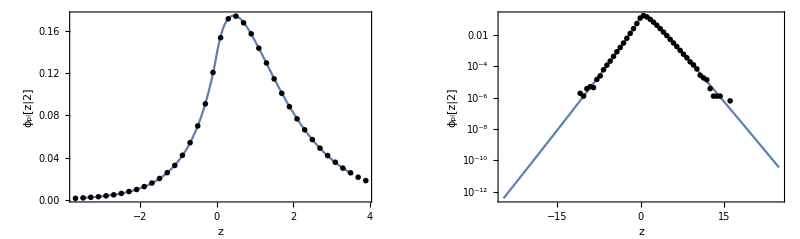

```mathematica
With[{u0=plotu0,α=plota,Σt=plotmut,n=plotn},
If[Length[inf3Ddeltaplaneisoscatter`simulations]>0,
Module[{maxz,dz,pointsϕ,plotpointsϕ,logplotϕ,plotϕ,exact1points},
data=SelectFirst[inf3Ddeltaplaneisoscatter`simulations,#[[1]]==α&&#[[2]]==Σt&&#[[3]]==u0&][[4]];
maxz=data[[2,5]];
dz=data[[2,7]];

pointsϕ = data[[10+inf3Ddeltaplaneisoscatter`numcollorders+n]];

(* divide by Σt to convert collision density into fluence *)
plotpointsϕ=inf3Ddeltaplaneisoscatter`ppoints[pointsϕ,dz,maxz,Σt];

exact1points=Quiet[{#[[1]], inf3Ddeltaplaneisoscatter`ϕexact[#[[1]],Σt,α,u0,n]}]& /@plotpointsϕ;

numpoints=Length[plotpointsϕ];
skip=Floor[numpoints 6/7 1/2];

plotϕ=Quiet[Show[
Plot[inf3Ddeltaplaneisoscatter`ϕexact[z,Σt,α,u0,n],{z,-maxz/7,maxz/7},PlotRange->All],
ListPlot[plotpointsϕ[[skip;;-skip]],PlotRange->All,PlotStyle->{Black,PointSize[.01]}],
Frame->True,
FrameLabel->{{ "ϕ_pl[z|"<>ToString[n]<>"]",},{z,}},PlotRange->All
]];
logplotϕ=Quiet[Show[
ListLogPlot[exact1points,PlotRange->All,Joined->True],
ListLogPlot[plotpointsϕ[[1;;-1;;3]],PlotRange->All,PlotStyle->{Black,PointSize[.01]}],
Frame->True,
FrameLabel->{{  "ϕ_pl[z|"<>ToString[n]<>"]",},{z,}},PlotRange->All
]];
Show[GraphicsGrid[{{plotϕ,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution 1 (thin)\nInfinite 3D, delta plane source, isotropic scattering, n-th scattered fluence ϕ_pl[z|"<>ToString[n]<>"], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", u_0 = "<>ToString[u0]]
]
,
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
]
```

### Radiance - Exact (Fourier Transform)

```mathematica
Manipulate[
If[Length[inf3Ddeltaplaneisoscatter`simulations]>0,
Module[{data,numorders,pointsu,plotpointsu,du,r,dz,maxz,zsim},
data=SelectFirst[inf3Ddeltaplaneisoscatter`simulations,#[[1]]==α&&#[[2]]==Σt&&#[[3]]==u0&][[4]];
numorders=data[[2,13]];
du=data[[2,9]];
dz=data[[2,7]];
maxz=data[[2,5]];

pointsu =data[[9+2 numorders+n]];

zsim = dz * n-0.5 dz-maxz;

plotpointsu=inf3Ddeltaplaneisoscatter`ppointsu[pointsu,du,Σt];
Quiet[Show[
ListPlot[plotpointsu,PlotRange->All,PlotStyle->Black,
Frame->True,
FrameLabel->{{ Pi L[zsim,u],},{u,}}],
Plot[Pi inf3Ddeltaplaneisoscatter`LexactCollidedFourier[zsim,u,Σt,α,u0],{u,-1,1}],
PlotLabel->"Infinite 3D Medium, isotropic plane source, isotropic scattering\nAngular distribution: Exact Fourier Transform solution\nπ L[z,u], z = "<>ToString[zsim]<>", α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", u_0 = "<>ToString[u0]
]]

],
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,
{{α,0.5},inf3Ddeltaplaneisoscatter`alphas},
{{Σt,1},inf3Ddeltaplaneisoscatter`muts},
{{u0,0.5},inf3Ddeltaplaneisoscatter`u0s},
{{n,122},Range[If[NumberQ[inf3Ddeltaplaneisoscatter`numz],inf3Ddeltaplaneisoscatter`numz,1]]}]
```

### Radiance, Rigorous Diffusion Approximation

```mathematica
Manipulate[
If[Length[inf3Ddeltaplaneisoscatter`simulations]>0,
Module[{data,numorders,pointsu,plotpointsu,du,r,dz,maxz,zsim},
data=SelectFirst[inf3Ddeltaplaneisoscatter`simulations,#[[1]]==α&&#[[2]]==Σt&&#[[3]]==u0&][[4]];
numorders=data[[2,13]];
du=data[[2,9]];
dz=data[[2,7]];
maxz=data[[2,5]];

pointsu =data[[9+2 numorders+n]];

zsim = dz * n-0.5 dz-maxz;

plotpointsu=inf3Ddeltaplaneisoscatter`ppointsu[pointsu,du,Σt];
Show[
ListPlot[plotpointsu,PlotRange->All,PlotStyle->Black,
Frame->True,
FrameLabel->{{ Pi L[zsim,u],},{u,}}],
Plot[Pi inf3Ddeltaplaneisoscatter`LrigorousDiffusion[zsim,u,Σt,α,Max[0.001,Min[u0,0.999]]
],{u,-1,1},PlotRange->All],
PlotLabel->"Infinite 3D Medium, isotropic plane source, isotropic scattering\nAngular distribution: Rigorous Diffusion Approximation\nπ L[z,u], z = "<>ToString[zsim]<>", α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", u_0 = "<>ToString[u0]
]

],
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,
{{α,0.5},inf3Ddeltaplaneisoscatter`alphas},
{{Σt,1},inf3Ddeltaplaneisoscatter`muts},
{{u0,0.5},inf3Ddeltaplaneisoscatter`u0s},
{{n,122},Range[If[NumberQ[inf3Ddeltaplaneisoscatter`numz],inf3Ddeltaplaneisoscatter`numz,1]]}]
```